```mathematica
F[t_]:=Sin[ω t]
ExactSolution[t_,x0_,v0_,k_,ζ_]=x[t]/.DSolve[{x''[t]==-ζ x'[t]-k x[t],x[0]==x0,x'[0]==v0},x[t],t][[1]];
Exact[ts_,x0_,v0_,ω_,ζ_]:=(
Re[N@ExactSolution[#,x0,v0,ω,ζ]]&/@ts
)

Euler[dt_,n_,x0_,v0_,ω_,ζ_]:=(
NestList[{#[[1]]+dt #[[2]],#[[2]]+dt( -ω#[[1]]-ζ#[[2]]),#[[3]]+dt}&,{x0,v0,0.0},n]
);
LeapFrog[dt_,n_,x0_,v0_,k_,ζ_]:=(

NestList[(v=((1-ζ dt/2.0)#[[2]]-dt k #[[1]])/(1+ζ dt/2.0);
{#[[1]]+dt v, v,#[[3]]+dt})&,{x0,v0,0},n])

MethodError[method_,dt_,k_,ζ_]:=Module[{nsteps},
nsteps=Round[100/dt];
sol=method[dt,nsteps,0,1,k,ζ];
sole=Exact[sol[[All,3]],0,1,k,ζ];
RootMeanSquare[sol[[All,1]]-sole]

(*ListPlot[{sol[[All,1]],sole},PlotRange->Full]*)
]
(* Stability analysis for fixed time step *)
(*DensityPlot[MethodError[Euler,0.5,k,ζ],{k,0.1,5},{ζ,0.1,5},MaxRecursion->0,PlotPoints->10]*)
MethodErrorGraph[method_]:=(
Print[ArrayPlot[Table[Log[MethodError[method,1,k,ζ]],{ζ,5,0.1,-.1},{k,0.1,5,.1}],
DataRange->{{0.1,5},{0.1,5}},FrameTicks->Automatic,PlotLegends->Automatic,FrameLabel->{"ζ","k"}]];

Print[ListPlot[Table[Log[MethodError[method,1,k,1]],{k,0.1,5,.1}],DataRange->{0.1,5},
PlotRange->{-5,3}]];
)
```

-Graphics-

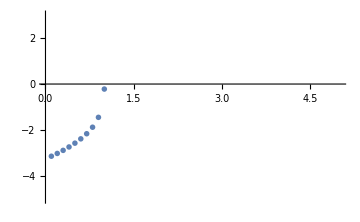

```mathematica
MethodErrorGraph[Euler]
```

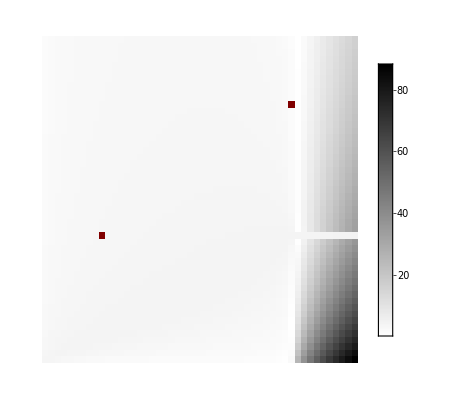

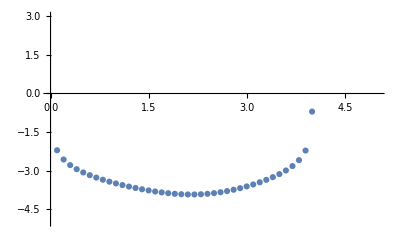

```mathematica
MethodErrorGraph[LeapFrog]
```

```mathematica
Atan2
```